```mathematica
RSolve[{(3a[n-1]+1)/(2a[n-1])==a[n],a[1]==2},a[n],n]
```

{{a[n]→(-5 (3/2-(√17)/2)^n+√17 (3/2-(√17)/2)^n+5 (3/2+(√17)/2)^n+√17 (3/2+(√17)/2)^n)/(-(3/2-(√17)/2)^n+√17 (3/2-(√17)/2)^n+(3/2+(√17)/2)^n+√17 (3/2+(√17)/2)^n)}}

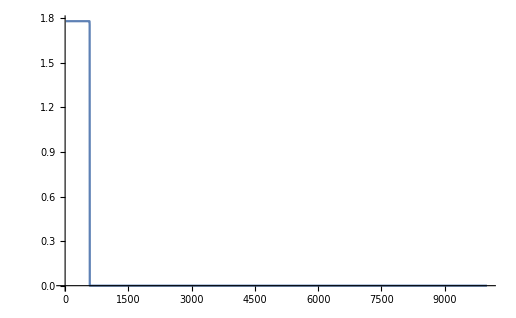

```mathematica
Plot[(-5 (3/2-(√17)/2)^n+√17 (3/2-(√17)/2)^n+5 (3/2+(√17)/2)^n+√17 (3/2+(√17)/2)^n)/(-(3/2-(√17)/2)^n+√17 (3/2-(√17)/2)^n+(3/2+(√17)/2)^n+√17 (3/2+(√17)/2)^n),{n,2,10000}]
```

```mathematica
Limit[(-5 (3/2-(√17)/2)^n+√17 (3/2-(√17)/2)^n+5 (3/2+(√17)/2)^n+√17 (3/2+(√17)/2)^n)/(-(3/2-(√17)/2)^n+√17 (3/2-(√17)/2)^n+(3/2+(√17)/2)^n+√17 (3/2+(√17)/2)^n),n->Infinity]
```

1/4 (3+√17)